Relativistic plasma aperture for laser intensity enhancement

M. Jirka, O. Klimo, M. Matys

Notebook on Github
Óscar Amaro, June 2021 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## Style

```mathematica
fntsz=20;
imgsz=400;
```

## Contribution of N harmonics

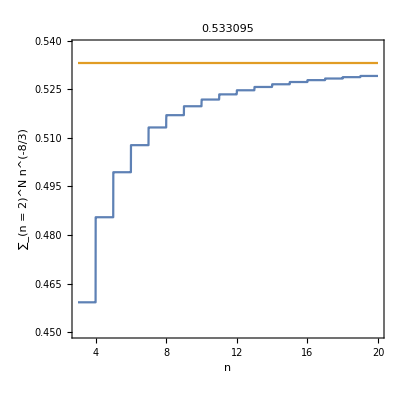

```mathematica
Clear[g,Ν,glim,n,g10]
g[Ν_]:=Sqrt[Sum[n^(-8/3),{n,2,Ν}]]
g10=g[10];
glim=Limit[g[Ν],Ν->∞]//N;
Plot[{g[Ν],glim},{Ν,3,20},PlotRange->{0.45,1.01glim},Frame->True,Axes->False,FrameStyle->Directive[Black],AspectRatio->1,FrameLabel->{Style["n",Black,fntsz],Style["∑_(n = 2)^Ν n^(-8/3)",Black,fntsz]},PlotLabel->Style[glim,Black,fntsz],FrameTicksStyle->fntsz,ImageSize->imgsz]
```

## Figure 4 a: find l such that fs=fp

(9 Abs[Log[(30000000000 l π)/3703]])/(1000000 √Abs[17.0523+Log[l^2/(2.54797×10^-8+1. l)]] √Log[4])

1.5×10^-6 √Abs[Log[(2.54517×10^7 l^2)/(2.54797×10^-8+1. l)]] Tan[0.688512+ArcCos[1/2 (0.772192+(2.27981×10^-18)/(√(l^4/(1.92398×10^35 l^4+(9+3.53223×10^8 l)^2))))]]

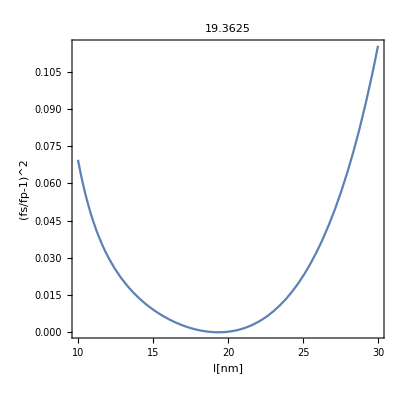

```mathematica
Clear[a0max,a0t,wmin,θ,wavg,fs,ψ,θ2nd,γavg,β,fp]
Clear[τ,W0,λ,c,ω0,a0,k0,np,nc]

(*equation 1*)
a0max=(np π l)/(nc λ);

(*equation 3*)
a0t=(4/3 √2 k0^2 l^2 np)/((3/4+8/3√2 k0 l)nc);

(*equation 6*)
wmin=W0 Sqrt[Abs[Log[a0max/a0]]];

(*equation 7*)
θ=ArcTan[(τ c)/(Sqrt[2Log[2]] W0)wmin/wavg];

(*equation 8*)
wavg=W0 Sqrt[Abs[Log[a0t/a0]]];

(*equation 9*)
fs=wmin Tan[θ];

(*equation 10*)
ψ=ArcTan[(τ c)/(Sqrt[2Log[2]] W0)];

(*equation 11*)
θ2nd=ArcCos[(1+β Cos[ψ/2])/(2β)];

(* after equation 11 *)
γavg=Sqrt[1+(a0t)^2/2];
β=Sqrt[1-1/(γavg)^2];

(*equation 12*)
fp=wavg Tan[θ2nd+ψ/2]//Simplify;


(*parameters*)
τ=30 10^-15;(*s*)
W0=1.5 10^-6;(*m*)
λ=805 10^-9;(*m*)
c= 3 10^8;(*m/s*)
ω0=2π c/λ//N;(*rad/s*)
a0=69;(**)
k0=ω0/c;(*1/m*)
np=450nc;(**)

fs=fs//Simplify
fp=fp//Simplify

leq=FindMinimum[(fs/fp-1)^2,{l,10 10^-9}][[2,1,2]];
Plot[(fs/fp-1)^2/.{l->ll  10^-9},{ll,10,30 },Frame->True,Axes->False,FrameStyle->Directive[Black],AspectRatio->1,FrameLabel->{Style["l[nm]",Black,fntsz],Style["(fs/fp-1)^2",Black,fntsz]},PlotLabel->Style[leq 10^9,Black,fntsz],ImageSize->imgsz,FrameTicksStyle->fntsz]
```

## Figure 4 b: harmonics I ∝ n^(-8/3) → E ∝ n^(-4/3)

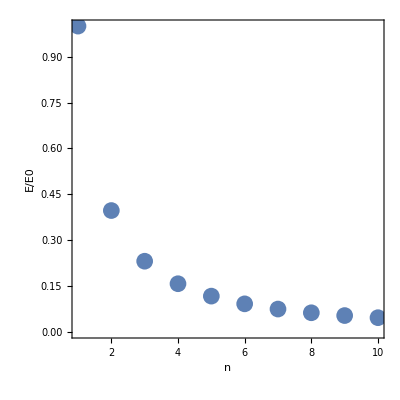

```mathematica
Clear[n]
ListPlot[Table[{n,n^(-4/3)},{n,1,10}],PlotRange->{{1,10},{0,1}},Frame->True,Axes->False,FrameStyle->Directive[Black],AspectRatio->1,FrameLabel->{Style["n",Black,fntsz],Style["E/E0",Black,fntsz]},PlotStyle->PointSize[0.03],FrameTicksStyle->fntsz,ImageSize->imgsz]
```

## Figure 6: Maximum I

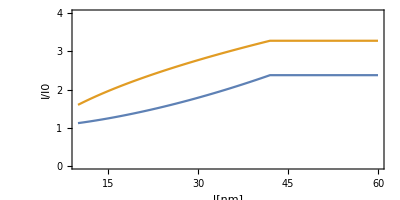

```mathematica
Clear[a0max,a0t,wmin,θ,wavg,fs,ψ,θ2nd,γavg,β,fp]
Clear[τ,W0,λ,c,ω0,a0,k0,np,nc]
Clear[I0,λ,lskin,a0pfun,a0sfun,a0ptop,a0stop]

I0=10^22;(*W/cm^2*)
λ=10^-6;(*m*)

(*def*)
a0=0.8855 Sqrt[I0/10^18] λ/10^-6;

(*equation 1*)
a0max=(np π l)/(nc λ);

(*equation 6*)
wmin=W0 Sqrt[Abs[Log[a0max/a0]]];

(*equation 3*)
a0t=(4/3 √2 k0^2 l^2 np)/((3/4+8/3√2 k0 l)nc);

(*equation 4*)
a0s=2a0 Exp[-r^2/(2W0)^2]/.{r->wmin};

(*equation 5*)
a0p=2g10 a0t+a0;

(*parameters*)
τ=30 10^-15;(*s*)
W0=1.5 10^-6;(*m*)
λ=805 10^-9;(*m*)
c= 3 10^8;(*m/s*)
ω0=2π c/λ//N;(*rad/s*)
k0=ω0/c;(*1/m*)
np=450nc;(**)

lskin=42 10^-9;
a0ptop=(a0p/a0)^2/.{l->lskin};
a0pfun=((a0p/a0)^2 HeavisideTheta[lskin-l]+a0ptop HeavisideTheta[l-lskin]);

a0stop=(a0s/a0)^2/.{l->lskin};
a0sfun=((a0s/a0)^2 HeavisideTheta[lskin-l]+a0stop HeavisideTheta[l-lskin]);

fntsz=20;
Plot[{a0pfun/.{l->ll  10^-9},a0sfun/.{l->ll  10^-9}},{ll,10,60 },Frame->True,Axes->False,FrameStyle->Directive[Black],AspectRatio->1/2,FrameLabel->{Style["l[nm]",Black,fntsz],Style["I/I0",Black,fntsz]},PlotRange->{0,4},FrameTicksStyle->fntsz,ImageSize->imgsz]
```